### Start choosing the example:

```mathematica
t=1;
```

```mathematica
(*beta=1;A=1;
(*DataIn=*){{1,1}},
(*FinalCosts=*){{1,2}},
(*SwitchingCostsData=*){}},*)
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];//Timing
v0=MFGEquations["criticalreduced1"][[2]]
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Done.

{0.013765,Null}

<|j280→1,u289→2,j281→1,j282→0,j283→0,jt284→1,jt285→0,u287→2,u288→2,u286→2|>

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort//Values
MFGEquations["criticalreduced2"][[2]]//KeySort//Values
```

{1,1,0,0,1,0,2,2,2,2}

{1,1,0,0,1,0,2,u286,2}

```mathematica
MFGEquations["reduced1"][[2]]//KeySort//Values
MFGEquations["reduced2"][[2]]//KeySort//Values
```

{1,1,0,0,1,0,2,2,2,2}

{1,1,0,0,1,0,2,u286,2}

#### Non-linear case with alpha != 1

```mathematica
Parameters["alpha"]=0;
Parameters
```

<|alpha→0,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$2348[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$2348[x$]-g$2348[m$]]|>

```mathematica
sol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],1, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

<|j280→1,u289→2,j281→1,j282→0,j283→0,jt284→1,jt285→0,u287→2,u288→2,u286→2|>

Note that 5 iterations work for the X2 solver tools:

```mathematica
sol2 = FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],3, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]
<10^(-6)&)]
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.sol2]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: True

Norm::nvm: The first Norm argument should be a scalar, vector, or matrix.

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: True

Norm::nvm: The first Norm argument should be a scalar, vector, or matrix.

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: True

Norm::nvm: The first Norm argument should be a scalar, vector, or matrix.

General::stop: Further output of Norm::nvm will be suppressed during this calculation.

<|j280→1,u289→2,j281→1,j282→0,j283→0,jt284→1,jt285→0,u287→2,u288→u286|>

Norm::nvm: The first Norm argument should be a scalar, vector, or matrix.

Norm[{}]

But if we try one more iteration, the next system is False. Now we have to create a way to deal with this.

```mathematica
sol26It=FixedPoint[FixedSolverStepX2[MFGEquations], 
MFGEquations["criticalreduced2"][[2]],8, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#2]
<10^(-6)&)]
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.%]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: True

Norm::nvm: The first Norm argument should be a scalar, vector, or matrix.

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: True

Norm::nvm: The first Norm argument should be a scalar, vector, or matrix.

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: True

Norm::nvm: The first Norm argument should be a scalar, vector, or matrix.

General::stop: Further output of Norm::nvm will be suppressed during this calculation.

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: True

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: True

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: True

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: True

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: True

<|j280→1,u289→2,j281→1,j282→0,j283→0,jt284→1,jt285→0,u287→2,u288→u286|>

Norm::nvm: The first Norm argument should be a scalar, vector, or matrix.

Norm[{}]

```mathematica
sol36It=Catch @ FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#2]
<10^(-6)&)]
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.%]
```

FixedX3: next step: True

Norm::nvm: The first Norm argument should be a scalar, vector, or matrix.

FixedX3: next step: True

Norm::nvm: The first Norm argument should be a scalar, vector, or matrix.

FixedX3: next step: True

Norm::nvm: The first Norm argument should be a scalar, vector, or matrix.

General::stop: Further output of Norm::nvm will be suppressed during this calculation.

FixedX3: next step: True

FixedX3: next step: True

FixedX3: next step: True

<|j280→1,u289→2,j281→1,j282→0,j283→0,jt284→1,jt285→0,u287→2,u288→u286|>

Norm::nvm: The first Norm argument should be a scalar, vector, or matrix.

Norm[{}]

#### Non-linear case with alpha = 1

```mathematica
Parameters["alpha"]=1;
Parameters
```

<|alpha→1,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$2348[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$2348[x$]-g$2348[m$]]|>

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]//KeySort//Values
```

{1,1,0,0,1,0,2,2,2,2}

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]//KeySort//Values
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: True

{1,1,0,0,1,0,2,u286,2}

```mathematica
nsol3=FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced2"][[2]],9, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-9)&)]//KeySort//Values
```

FixedX3: next step: True

{1,1,0,0,1,0,2,u286,2}

### What is this plot for?

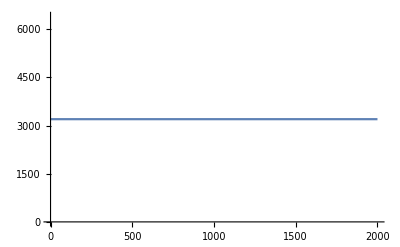
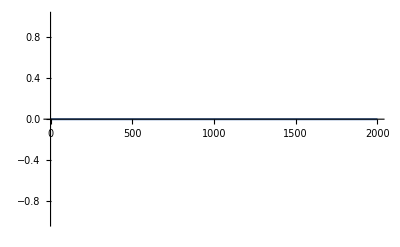
<|{2,1->2}→-Graphics-,{ex81,2->ex81}→-Graphics-,{1,en80->1}→-Graphics-,{1,1->2}→-Graphics-,{2,2->ex81}→-Graphics-,{en80,en80->1}→-Graphics-|>

```mathematica
Function[a,ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-a/(m^(1-alpha)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will always retrieve the most up - to - date values.